```mathematica
(*Tunneling Density of States*)
Des=0.6285;Ded=1.582;Qx=(2 π)/5;
ClearAll[f]
f[k_,eps0_,eps1_,eps2_,Δ1_,Δ2_]:=With[{ω=Exp[(2 π I)/3],t1=2^(1/3),t2=2^(2/3)},Module[{A,B,disc,c},A=9 Δ1^2 eps0+9 Δ2^2 eps0+2 eps0^3-9 Δ1^2 eps1+18 Δ2^2 eps1+3 eps0^2 eps1-3 eps0 eps1^2-2 eps1^3+18 Δ1^2 eps2-9 Δ2^2 eps2+3 eps0^2 eps2+12 eps0 eps1 eps2+3 eps1^2 eps2-3 eps0 eps2^2+3 eps1 eps2^2-2 eps2^3;
B=-(eps0-eps1-eps2)^2-3 (Δ1^2+Δ2^2+eps0 eps1+eps0 eps2-eps1 eps2);
disc=Sqrt[A^2+4 B^3];
c=(A+disc)^(1/3);
(eps0-eps1-eps2)/3+(ω^k*c-ω^(-k)*t2*B/c)/(3*t1)]]

Factor1[E1_,E2_,E3_,eps1_,eps2_]:=(E1+eps1) (E1+eps2)/((E1-E2) (E1-E3))

Factor2[E1_,E2_,E3_,eps1_,Δ_]:=Δ*(E1+eps1)/((E1-E2) (E1-E3))

t=1;tprime=0.3 t;
Qy=0;mu=-0.5;
Dispersion[x_,y_]:=-2 t (Cos[x]+Cos[y])+4 tprime Cos[x] Cos[y]-mu;

Jx[x_,y_]:=2 t Sin[x]-4 Cos[y] Sin[x] tprime;
Jy[x_,y_]:=2 t Sin[y]-4 Cos[x] Sin[y] tprime;

Shaped[x_,y_]:=Cos[x]-Cos[y];
Shapes[x_,y_]:=Cos[x]+Cos[y];
Netshape[x_,y_]:=Des*Shapes[x-Qx/2,y]+Ded*Shaped[x-Qx/2,y];
fepsi[x_,y_]:=Dispersion[x,y];
fepsi1[x_,y_]:=Dispersion[x-Qx,y-Qy];
fepsi2[x_,y_]:=Dispersion[x+Qx,y+Qy];

Band1[x_,y_]:=f[1,fepsi[x,y],fepsi1[x,y],fepsi2[x,y],Des*Shapes[x-Qx/2,y]+Ded*Shaped[x-Qx/2,y],Des*Shapes[x+Qx/2,y]+Ded*Shaped[x+Qx/2,y]];
Band2[x_,y_]:=f[2,fepsi[x,y],fepsi1[x,y],fepsi2[x,y],Des*Shapes[x-Qx/2,y]+Ded*Shaped[x-Qx/2,y],Des*Shapes[x+Qx/2,y]+Ded*Shaped[x+Qx/2,y]];
Band3[x_,y_]:=f[3,fepsi[x,y],fepsi1[x,y],fepsi2[x,y],Des*Shapes[x-Qx/2,y]+Ded*Shaped[x-Qx/2,y],Des*Shapes[x+Qx/2,y]+Ded*Shaped[x+Qx/2,y]];

Thermal[E_,T_]:=1/(Exp[E/T]+1);

DiracN[x_,sigma_]:=1/(Sqrt[2 Pi sigma]) Exp[-(x^2)/(2 sigma)];
ThermalD[x_,T_]:=-ⅇ^(x/T)/((1+ⅇ^(x/T))^2 T); 

IntGG[T_,px_,py_]:=Module[{result0,result1,result,g1n,g2n,g3n,
cy0,cy,fre,kx,ky,pxp,pxn,pyp,pyn,E1p,E2p,E3p,E1n,E2n,E3n,eps1p,eps2p,eps1n,eps2n},
kx=1/10^7;ky=0; fre=0;
pxp=px+kx/2;pxn=px-kx/2;
pyp=py+ky/2;pyn=py-ky/2;
E1p=Band1[pxp,pyp];E2p=Band2[pxp,pyp];E3p=Band3[pxp,pyp];
Ep={E1p,E2p,E3p};
E1n=Band1[pxn,pyn];E2n=Band2[pxn,pyn];E3n=Band3[pxn,pyn];
En={E1n,E2n,E3n};
(**)
eps1p=fepsi1[pxp,pyp];eps2p=fepsi2[pxp,pyp];
eps1n=fepsi1[pxn,pyn];eps2n=fepsi2[pxn,pyn];
(**)
g1n=Factor1[E1n,E2n,E3n,eps1n,eps2n];g2n=Factor1[E2n,E1n,E3n,eps1n,eps2n];g3n=Factor1[E3n,E1n,E2n,eps1n,eps2n];
g1p=Factor1[E1p,E2p,E3p,eps1p,eps2p];g2p=Factor1[E2p,E1p,E3p,eps1p,eps2p];g3p=Factor1[E3p,E1p,E2p,eps1p,eps2p];
dis1n=Thermal[E1n,T];dis2n=Thermal[E2n,T];dis3n=Thermal[E3n,T];
dis1p=Thermal[E1p,T];dis2p=Thermal[E2p,T];dis3p=Thermal[E3p,T];
(**)
gn={g1n,g2n,g3n};gp={g1p,g2p,g3p};
disn={dis1n,dis2n,dis3n};disp={dis1p,dis2p,dis3p};
(**)
result0=Sum[If[i!=j,(disp[[j]]-disn[[i]])/(Ep[[j]]-En[[i]])*gn[[i]]*gp[[j]],0],{i,1,3},{j,1,3}];
result1=Sum[ThermalD[En[[i]],T]*gn[[i]]*gn[[i]],{i,1,3}];
result=result0+result1;
(*now let us add the current operator*)
cx=Jx[px,py];cy=Jy[px,py];
(*For definiteness let us consider y-direction response*)
Result=result*cy*cy
]

IntGGIntegrated[T_]:=NIntegrate[IntGG[T,px,py],{px,-Pi,Pi},{py,-Pi,Pi}, Method->{"LocalAdaptive"}];


IntFF[T_,px_,py_]:=Module[{result0,result1,result,cy0,cy,Pshape,Nshape,order,fre,kx,ky,pxp,pxn,pyp,pyn,E1p,E2p,E3p,E1n,E2n,E3n,eps1p,eps2p,eps1n,eps2n},
kx=1/10^7;ky=0; fre=0;
pxp=px+kx/2;pxn=px-kx/2;
pyp=py+ky/2;pyn=py-ky/2;
E1p=Band1[pxp,pyp];E2p=Band2[pxp,pyp];E3p=Band3[pxp,pyp];
Ep={E1p,E2p,E3p};
E1n=Band1[pxn,pyn];E2n=Band2[pxn,pyn];E3n=Band3[pxn,pyn];
En={E1n,E2n,E3n};
eps1p=fepsi1[pxp,pyp];eps2p=fepsi2[pxp,pyp];
eps1n=fepsi1[pxn,pyn];eps2n=fepsi2[pxn,pyn];
(**)
Pshape=Des*Shapes[pxp+Qx/2,pyp]+Ded*Shaped[pxp+Qx/2,pyp];
Nshape=Des*Shapes[pxn+Qx/2,pyn]+Ded*Shaped[pxn+Qx/2,pyn];
(**)
g1n=Factor2[E1n,E2n,E3n,eps1n,Nshape];g2n=Factor2[E2n,E1n,E3n,eps1n,Nshape];g3n=Factor2[E3n,E1n,E2n,eps1n,Nshape];
g1p=Factor2[E1p,E2p,E3p,eps1p,Pshape];g2p=Factor2[E2p,E1p,E3p,eps1p,Pshape];g3p=Factor2[E3p,E1p,E2p,eps1p,Pshape];
(**)
dis1n=Thermal[E1n,T];dis2n=Thermal[E2n,T];dis3n=Thermal[E3n,T];
dis1p=Thermal[E1p,T];dis2p=Thermal[E2p,T];dis3p=Thermal[E3p,T];
(**)
gn={g1n,g2n,g3n};gp={g1p,g2p,g3p};
disn={dis1n,dis2n,dis3n};disp={dis1p,dis2p,dis3p};
(**)
result0=Sum[If[i!=j,(disp[[j]]-disn[[i]])/(Ep[[j]]-En[[i]])*gn[[i]]*gp[[j]],0],{i,1,3},{j,1,3}];
result1=Sum[ThermalD[En[[i]],T]*gn[[i]]*gn[[i]],{i,1,3}];
result=result0+result1;
(**)
(*now let us add the current operator*)
cy0=Jy[px,py];cy=Jy[px+Qx,py+Qy];
(*For definiteness let us consider y-direction response*)
Result=result*cy*cy0
]
IntFFIntegrated[T_]:=NIntegrate[IntFF[T,px,py],{px,-Pi,Pi},{py,-Pi,Pi}, Method->{"LocalAdaptive"}];





IntFF1[T_,px_,py_]:=Module[{result0,result1,result,cy0,cy,Pshape,Nshape,order,fre,kx,ky,pxp,pxn,pyp,pyn,E1p,E2p,E3p,E1n,E2n,E3n,eps1p,eps2p,eps1n,eps2n},
kx=1/10^7;ky=0; fre=0;
pxp=px+kx/2;pxn=px-kx/2;
pyp=py+ky/2;pyn=py-ky/2;
E1p=Band1[pxp,pyp];E2p=Band2[pxp,pyp];E3p=Band3[pxp,pyp];
Ep={E1p,E2p,E3p};
E1n=Band1[pxn,pyn];E2n=Band2[pxn,pyn];E3n=Band3[pxn,pyn];
En={E1n,E2n,E3n};
eps1p=fepsi1[pxp,pyp];eps2p=fepsi2[pxp,pyp];
eps1n=fepsi1[pxn,pyn];eps2n=fepsi2[pxn,pyn];
(**)
Pshape=Des*Shapes[pxp-Qx/2,pyp]+Ded*Shaped[pxp-Qx/2,pyp];
Nshape=Des*Shapes[pxn-Qx/2,pyn]+Ded*Shaped[pxn-Qx/2,pyn];
(**)
g1n=Factor2[E1n,E2n,E3n,eps2n,Nshape];g2n=Factor2[E2n,E1n,E3n,eps2n,Nshape];g3n=Factor2[E3n,E1n,E2n,eps2n,Nshape];
g1p=Factor2[E1p,E2p,E3p,eps2p,Pshape];g2p=Factor2[E2p,E1p,E3p,eps2p,Pshape];g3p=Factor2[E3p,E1p,E2p,eps2p,Pshape];
(**)
dis1n=Thermal[E1n,T];dis2n=Thermal[E2n,T];dis3n=Thermal[E3n,T];
dis1p=Thermal[E1p,T];dis2p=Thermal[E2p,T];dis3p=Thermal[E3p,T];
(**)
gn={g1n,g2n,g3n};gp={g1p,g2p,g3p};
disn={dis1n,dis2n,dis3n};disp={dis1p,dis2p,dis3p};
(**)
result0=Sum[If[i!=j,(disp[[j]]-disn[[i]])/(Ep[[j]]-En[[i]])*gn[[i]]*gp[[j]],0],{i,1,3},{j,1,3}];
result1=Sum[ThermalD[En[[i]],T]*gn[[i]]*gp[[i]],{i,1,3}];
result=result0+result1;
(**)
(*now let us add the current operator*)
cy0=Jy[px,py];cy=Jy[px-Qx,py-Qy];
(*For definiteness let us consider y-direction response*)
Result=result*cy*cy0
]
IntFF1Integrated[T_]:=NIntegrate[IntFF1[T,px,py],{px,-Pi,Pi},{py,-Pi,Pi}, Method->{"LocalAdaptive"}];
```

```mathematica
IntGGIntegrated[0.008]
IntFFIntegrated[0.008]
IntFF1Integrated[0.008]
```

-5.92099+9.89311×10^-16 ⅈ

1.81442

1.81442

```mathematica
2*1.8144204272004865+5.920993408470262
```

9.54983

```mathematica
IntGGIntegrated[0.008]
IntFFIntegrated[0.008]
```

-5.92099+9.89311×10^-16 ⅈ

1.81442

```mathematica
Gc=Table[ IntGGIntegrated[x],{x,0.008,1,0.01}]
Fc=Table[ IntFFIntegrated[x],{x,0.008,1,0.01}]
```

{-5.92099+9.89311×10^-16 ⅈ,-5.92129+8.36886×10^-16 ⅈ,-5.92114+9.12724×10^-16 ⅈ,-5.92093+9.72466×10^-16 ⅈ,-5.92099+1.09708×10^-15 ⅈ,-5.92031+9.61806×10^-16 ⅈ,-5.9199+1.02598×10^-15 ⅈ,-5.91942+1.00376×10^-15 ⅈ,-5.91887+9.60428×10^-16 ⅈ,-5.91826+9.94173×10^-16 ⅈ,-5.91756+1.00019×10^-15 ⅈ,-5.91683+9.40635×10^-16 ⅈ,-5.91603+9.13421×10^-16 ⅈ,-5.91518+9.40438×10^-16 ⅈ,-5.91428+9.29069×10^-16 ⅈ,-5.91337+8.81534×10^-16 ⅈ,-5.91243+9.46028×10^-16 ⅈ,-5.91149+9.33071×10^-16 ⅈ,-5.91055+9.85755×10^-16 ⅈ,-5.90965+9.85807×10^-16 ⅈ,-5.90881+9.86875×10^-16 ⅈ,-5.90803+9.26729×10^-16 ⅈ,-5.90735+9.31155×10^-16 ⅈ,-5.90679+9.37505×10^-16 ⅈ,-5.90638+8.45913×10^-16 ⅈ,-5.90615+8.39299×10^-16 ⅈ,-5.90612+8.74782×10^-16 ⅈ,-5.90633+8.69771×10^-16 ⅈ,-5.90667+9.34755×10^-16 ⅈ,-5.90759+8.87189×10^-16 ⅈ,-5.9087+9.11889×10^-16 ⅈ,-5.91019+9.11459×10^-16 ⅈ,-5.91206+9.07063×10^-16 ⅈ,-5.91435+9.06509×10^-16 ⅈ,-5.91708+8.89712×10^-16 ⅈ,-5.92029+8.97384×10^-16 ⅈ,-5.92399+9.08157×10^-16 ⅈ,-5.9282+9.0008×10^-16 ⅈ,-5.93294+8.18058×10^-16 ⅈ,-5.93822+8.17289×10^-16 ⅈ,-5.94406+8.16232×10^-16 ⅈ,-5.95047+8.13637×10^-16 ⅈ,-5.95745+8.12546×10^-16 ⅈ,-5.96501+8.11406×10^-16 ⅈ,-5.97314+8.08998×10^-16 ⅈ,-5.98186+8.07249×10^-16 ⅈ,-5.99115+8.00943×10^-16 ⅈ,-6.00102+7.9244×10^-16 ⅈ,-6.01145+7.95598×10^-16 ⅈ,-6.02244+7.97381×10^-16 ⅈ,-6.03397+8.02243×10^-16 ⅈ,-6.04604+8.21132×10^-16 ⅈ,-6.05862+8.11099×10^-16 ⅈ,-6.07171+8.07538×10^-16 ⅈ,-6.08529+8.40938×10^-16 ⅈ,-6.09935+8.36697×10^-16 ⅈ,-6.11385+8.28201×10^-16 ⅈ,-6.12878+8.30352×10^-16 ⅈ,-6.14414+8.18779×10^-16 ⅈ,-6.15988+8.07186×10^-16 ⅈ,-6.17599+8.17192×10^-16 ⅈ,-6.19245+8.11968×10^-16 ⅈ,-6.20924+8.06549×10^-16 ⅈ,-6.22633+8.00944×10^-16 ⅈ,-6.24371+8.14529×10^-16 ⅈ,-6.26134+8.08065×10^-16 ⅈ,-6.27922+7.84842×10^-16 ⅈ,-6.29729+7.78885×10^-16 ⅈ,-6.31559+7.713×10^-16 ⅈ,-6.33404+7.64346×10^-16 ⅈ,-6.35264+7.57282×10^-16 ⅈ,-6.37136+7.50117×10^-16 ⅈ,-6.3902+7.42858×10^-16 ⅈ,-6.40911+7.34137×10^-16 ⅈ,-6.42814+7.43329×10^-16 ⅈ,-6.44712+7.22715×10^-16 ⅈ,-6.46618+7.15087×10^-16 ⅈ,-6.48524+7.07404×10^-16 ⅈ,-6.50429+6.99673×10^-16 ⅈ,-6.52331+6.91902×10^-16 ⅈ,-6.54228+6.84097×10^-16 ⅈ,-6.56119+6.76265×10^-16 ⅈ,-6.58002+6.68412×10^-16 ⅈ,-6.59876+6.25427×10^-16 ⅈ,-6.61738+6.18157×10^-16 ⅈ,-6.63588+6.10874×10^-16 ⅈ,-6.65426+6.18012×10^-16 ⅈ,-6.67247+6.10472×10^-16 ⅈ,-6.69052+6.02944×10^-16 ⅈ,-6.70838+5.83585×10^-16 ⅈ,-6.72606+5.75629×10^-16 ⅈ,-6.74355+5.75153×10^-16 ⅈ,-6.76082+5.67919×10^-16 ⅈ,-6.77788+5.60706×10^-16 ⅈ,-6.79471+5.52898×10^-16 ⅈ,-6.81131+5.43764×10^-16 ⅈ,-6.82765+5.3661×10^-16 ⅈ,-6.84375+5.29492×10^-16 ⅈ,-6.85959+5.22412×10^-16 ⅈ,-6.87515+5.15373×10^-16 ⅈ}

{1.81442,1.81459,1.81489,1.81533,1.81591,1.81663,1.8175,1.81851,1.81968,1.82102,1.82251,1.82416,1.82596,1.82789,1.82993,1.83207,1.83428,1.83653,1.83882,1.84111,1.84337,1.8456,1.84774,1.84977,1.85169,1.85346,1.85506,1.85646,1.85765,1.85859,1.85927,1.85966,1.85975,1.85951,1.85894,1.858,1.8567,1.85502,1.85295,1.85048,1.8476,1.84431,1.84061,1.83648,1.83194,1.82698,1.82161,1.81582,1.80963,1.80303,1.79605,1.78867,1.78092,1.7728,1.76432,1.7555,1.74634,1.73686,1.72706,1.71696,1.70658,1.69592,1.685,1.67383,1.66243,1.6508,1.63897,1.62694,1.61472,1.60233,1.58978,1.57709,1.56426,1.5513,1.53823,1.52506,1.5118,1.49846,1.48505,1.47158,1.45806,1.44449,1.4309,1.41728,1.40364,1.39,1.37635,1.36271,1.34909,1.33548,1.32191,1.30836,1.29486,1.28139,1.26798,1.25462,1.24132,1.22809,1.21492,1.20182}

```mathematica
Gc={-5.920993408470262+9.893108605688631*^-16 ⅈ,-5.921293476571059+8.368860795017018*^-16 ⅈ,-5.921144882439638+9.12724327728054*^-16 ⅈ,-5.920934354074438+9.724658120416647*^-16 ⅈ,-5.920989624728926+1.0970842296603071*^-15 ⅈ,-5.920310131571373+9.618063866794541*^-16 ⅈ,-5.919898438357364+1.0259796665481565*^-15 ⅈ,-5.919420428915384+1.0037568628178208*^-15 ⅈ,-5.918873154309916+9.60427884155504*^-16 ⅈ,-5.91825810631838+9.941729614339164*^-16 ⅈ,-5.917563288744775+1.0001942226759588*^-15 ⅈ,-5.916832412186294+9.406352154254468*^-16 ⅈ,-5.91602858391912+9.134213028757462*^-16 ⅈ,-5.915178901319855+9.40437986507449*^-16 ⅈ,-5.914280789246965+9.290691325268403*^-16 ⅈ,-5.913365771615417+8.815343795706502*^-16 ⅈ,-5.912428157174135+9.460281356416258*^-16 ⅈ,-5.911487116845771+9.330707629697178*^-16 ⅈ,-5.910554978334456+9.857552725016942*^-16 ⅈ,-5.909654485899766+9.858073849192812*^-16 ⅈ,-5.908808978635882+9.868746054732796*^-16 ⅈ,-5.908032185890822+9.267292136638169*^-16 ⅈ,-5.907350894620844+9.311545687444767*^-16 ⅈ,-5.906788100516857+9.37505203421503*^-16 ⅈ,-5.906380707796217+8.459129933417592*^-16 ⅈ,-5.906145298338711+8.39299020951011*^-16 ⅈ,-5.906118303902048+8.747817520090906*^-16 ⅈ,-5.9063297399565275+8.697714413591106*^-16 ⅈ,-5.906665003004141+9.347545335210949*^-16 ⅈ,-5.907590695608514+8.871886016875456*^-16 ⅈ,-5.908704021812195+9.11889170706798*^-16 ⅈ,-5.910185084215078+9.114594122227307*^-16 ⅈ,-5.912056128217612+9.070626027898477*^-16 ⅈ,-5.914347148481777+9.065086986370845*^-16 ⅈ,-5.917084256218089+8.897115024280468*^-16 ⅈ,-5.920291586195388+8.973837582163927*^-16 ⅈ,-5.923991195511558+9.081572470592783*^-16 ⅈ,-5.928196381743753+9.0008041204106*^-16 ⅈ,-5.932937633178616+8.180577402725916*^-16 ⅈ,-5.938222927374764+8.172888389375721*^-16 ⅈ,-5.94406433501161+8.162318060187432*^-16 ⅈ,-5.950471493956935+8.13636530757624*^-16 ⅈ,-5.95744956413427+8.125460470772531*^-16 ⅈ,-5.965008525730283+8.114061956187516*^-16 ⅈ,-5.973144290754547+8.089982622058433*^-16 ⅈ,-5.981861821600624+8.072491210930998*^-16 ⅈ,-5.991154707151212+8.0094278996484*^-16 ⅈ,-6.001019524215808+7.924398082837538*^-16 ⅈ,-6.011449724628703+7.955983424735819*^-16 ⅈ,-6.022438426288916+7.973806717641756*^-16 ⅈ}
```

{-5.92099+9.89311×10^-16 ⅈ,-5.92129+8.36886×10^-16 ⅈ,-5.92114+9.12724×10^-16 ⅈ,-5.92093+9.72466×10^-16 ⅈ,-5.92099+1.09708×10^-15 ⅈ,-5.92031+9.61806×10^-16 ⅈ,-5.9199+1.02598×10^-15 ⅈ,-5.91942+1.00376×10^-15 ⅈ,-5.91887+9.60428×10^-16 ⅈ,-5.91826+9.94173×10^-16 ⅈ,-5.91756+1.00019×10^-15 ⅈ,-5.91683+9.40635×10^-16 ⅈ,-5.91603+9.13421×10^-16 ⅈ,-5.91518+9.40438×10^-16 ⅈ,-5.91428+9.29069×10^-16 ⅈ,-5.91337+8.81534×10^-16 ⅈ,-5.91243+9.46028×10^-16 ⅈ,-5.91149+9.33071×10^-16 ⅈ,-5.91055+9.85755×10^-16 ⅈ,-5.90965+9.85807×10^-16 ⅈ,-5.90881+9.86875×10^-16 ⅈ,-5.90803+9.26729×10^-16 ⅈ,-5.90735+9.31155×10^-16 ⅈ,-5.90679+9.37505×10^-16 ⅈ,-5.90638+8.45913×10^-16 ⅈ,-5.90615+8.39299×10^-16 ⅈ,-5.90612+8.74782×10^-16 ⅈ,-5.90633+8.69771×10^-16 ⅈ,-5.90667+9.34755×10^-16 ⅈ,-5.90759+8.87189×10^-16 ⅈ,-5.9087+9.11889×10^-16 ⅈ,-5.91019+9.11459×10^-16 ⅈ,-5.91206+9.07063×10^-16 ⅈ,-5.91435+9.06509×10^-16 ⅈ,-5.91708+8.89712×10^-16 ⅈ,-5.92029+8.97384×10^-16 ⅈ,-5.92399+9.08157×10^-16 ⅈ,-5.9282+9.0008×10^-16 ⅈ,-5.93294+8.18058×10^-16 ⅈ,-5.93822+8.17289×10^-16 ⅈ,-5.94406+8.16232×10^-16 ⅈ,-5.95047+8.13637×10^-16 ⅈ,-5.95745+8.12546×10^-16 ⅈ,-5.96501+8.11406×10^-16 ⅈ,-5.97314+8.08998×10^-16 ⅈ,-5.98186+8.07249×10^-16 ⅈ,-5.99115+8.00943×10^-16 ⅈ,-6.00102+7.9244×10^-16 ⅈ,-6.01145+7.95598×10^-16 ⅈ,-6.02244+7.97381×10^-16 ⅈ}

```mathematica
Fc={1.8144204272004865,1.8145890000932716,1.8148926391783986,1.815334153740134,1.8159128700124945,1.8166308566706006,1.8174950281753712,1.8185117358633285,1.8196848274154904,1.8210183614584352,1.8225127894880542,1.8241627132106273,1.8259588778217979,1.8278863336284732,1.8299312557582665,1.8320658331199402,1.8342757224176736,1.8365345801240736,1.8388198114251142,1.8411056748298376,1.8433684649313247,1.8456040030566063,1.8477437324875066,1.8497677320354486,1.8516882900405263,1.8534607913459622,1.855060966148152,1.856464714313609,1.8576491739009902,1.8585907273329862,1.8592676753790194,1.859659752379339,1.8597469291174094,1.8595113222279562,1.8589354941773637,1.8580044340045148,1.8567046145070285,1.8550230638110348,1.8529522833163963,1.8504806299432595,1.8476022528488105,1.8443120456698407,1.8406059497543947,1.8364820911278708,1.8319395798898317,1.8269814037022374,1.8216058594696016,1.8158197465105193,1.809626855006381,1.8030331182564188}
```

{1.81442,1.81459,1.81489,1.81533,1.81591,1.81663,1.8175,1.81851,1.81968,1.82102,1.82251,1.82416,1.82596,1.82789,1.82993,1.83207,1.83428,1.83653,1.83882,1.84111,1.84337,1.8456,1.84774,1.84977,1.85169,1.85346,1.85506,1.85646,1.85765,1.85859,1.85927,1.85966,1.85975,1.85951,1.85894,1.858,1.8567,1.85502,1.85295,1.85048,1.8476,1.84431,1.84061,1.83648,1.83194,1.82698,1.82161,1.81582,1.80963,1.80303}

```mathematica
diagm={9.566248905093502,9.566657565081364,9.567383025132793,9.56842866638622,9.569800475647757,9.571507368207179,9.573562569123732,9.575981793780466,9.578781707303545,9.581976141515753,9.585579655732557,9.589582499079238,9.593996164424556,9.598810002777293,9.604146757497308,9.60958879955825,9.61552128360461,9.621790527594039,9.62837522268784,9.635252944468347,9.642400480875855,9.649793739984156,9.657409027087962,9.665221610207022,9.673207001596538,9.681339746211833,9.689596678977793,9.697951575863609,9.706381507453148,9.71486188329896,9.723369288528463,9.731880386841304,9.740372551670195,9.74882367413005,9.757212379521123,9.765517708260205,9.773719641522256,9.781798927217176,9.789737040163871,9.797516231236695,9.805119640911617,9.812531278199778,9.819736048259903,9.826719723236259,9.833468762330849,9.839970737346885,9.846213869833244,9.85218715440874,9.857881086490547,9.863285603074502,9.868392225696727,9.873193405183574,9.877683035538173,9.881852984964588,9.885698455698574,9.889214834705028,9.892399565951623,9.895243756147927,9.897744115101393,9.899903115509835,9.901715903897907,9.903180545378014,9.904295840502442,9.90506079367344,9.905474894781829,9.905538017616745,9.905250370723609,9.904612531423602,9.903625360863813,9.90229115859711,9.900608085197561,9.898581240767292,9.896211063903422,9.893500309376368,9.890451197780873,9.887065693276208,9.883347309539174,9.879298705015836,9.874923009728459,9.870223428071764,9.865203297344788,9.859866142747872,9.854215431319295,9.848255073955029,9.84198867433922,9.835420169471018,9.828553523557044,9.821392604154866,9.813941575083119,9.806204483376984,9.798185576502714,9.789888989561392,9.781318960051241,9.77247969618594,9.763375581324185,9.75401085996711,9.744389840560565,9.734516855144578,9.724396185603913,9.714032244093467};
```

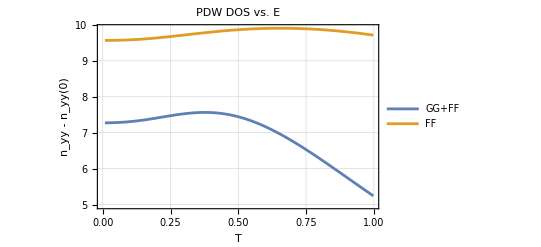

```mathematica
xValues=Range[0.008,1,0.01];
Para=Re[Gc+Fc*2];
Diag=Re[-Gc+Fc*2];
FFResponse=Re[(Fc*2)*2];
dataPara=Transpose[{xValues,Para+diagm}];
dataDiag=Transpose[{xValues,diagm}];
myplot2=ListPlot[{dataPara,dataDiag},PlotRange->All,Joined->True,Frame->True,GridLines->Automatic,FrameLabel->{Style["T",20,Bold],Style[Row[{Subscript["n","yy"]," - ",Subscript["n","yy"],"(0)"}],20,Bold]},PlotLabel->"PDW DOS vs. E",PlotLegends->{"GG+FF","FF","Diag"}]
```

```mathematica
Diag=Re[-Gc+Fc*2];
Export["Documents/fermion_part/data/diag.csv",Re[diagm]]
Export["Documents/fermion_part/data/result.csv",Re[Para+diagm]]
Export["Documents/fermion_part/data/x.csv",Re[xValues]]
```

Documents/fermion_part/data/diag.csv

Documents/fermion_part/data/result.csv

Documents/fermion_part/data/x.csv

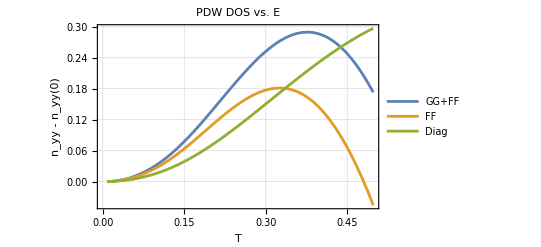

```mathematica
xValues=Range[0.008,0.5,0.01];
Response=Re[Gc+Fc*2+diagm];
FFResponse=Re[(Fc*2)*2];
data=Transpose[{xValues,Response-Response[[1]]}];
data1=Transpose[{xValues,FFResponse-FFResponse[[1]]}];
data2=Transpose[{xValues,diagm-diagm[[1]]}];
myplot2=ListPlot[{data,data1,data2},PlotRange->All,Joined->True,Frame->True,GridLines->Automatic,FrameLabel->{Style["T",20,Bold],Style[Row[{Subscript["n","yy"]," - ",Subscript["n","yy"],"(0)"}],20,Bold]},PlotLabel->"PDW DOS vs. E",PlotLegends->{"GG+FF","FF","Diag"}]
```

```mathematica
dataxx={{0.008,1.},{0.018000000000000002,1.000157614542517},{0.028,1.0002344583101654},{0.038,1.0006141434883276},{0.048,1.001235784067103},{0.058,1.0017332172826972},{0.068,1.0024474171496893},{0.07800000000000001,1.0033019665005105},{0.088,1.0042597093849468},{0.098,1.0053786500565463},{0.10800000000000001,1.0065448994431168},{0.118,1.0078917700284955},{0.128,1.0093698839340246},{0.138,1.0109933273813418},{0.14800000000000002,1.012758621183372},{0.158,1.0146723773291626},{0.168,1.0167241389068082},{0.17800000000000002,1.0189143941435985},{0.188,1.021204076380538},{0.198,1.023737288793512},{0.20800000000000002,1.0260892221485909},{0.218,1.0287293531733739},{0.228,1.0313419854931494},{0.23800000000000002,1.0339565676237783},{0.248,1.0365417040501606},{0.258,1.0390572879274995},{0.268,1.0414695419747657},{0.278,1.0437336877769068},{0.28800000000000003,1.0458037798952742},{0.298,1.047655788343601},{0.308,1.049248378734088},{0.318,1.050533243654346},{0.328,1.051478631415771},{0.338,1.0520299973722718},{0.34800000000000003,1.0522705059817412},{0.35800000000000004,1.0520389649706314},{0.368,1.051402063623985},{0.378,1.050266113831085},{0.388,1.0486877693033096},{0.398,1.0466414360811758},{0.40800000000000003,1.0441176315965954},{0.41800000000000004,1.0411166047955684},{0.428,1.0376399783175527},{0.438,1.0336953984478114},{0.448,1.0292905092860538},{0.458,1.0244360261016323},{0.468,1.019145258218861},{0.47800000000000004,1.0134352827344943},{0.488,1.0073228746262983},{0.498,1.000823981735429}};
```

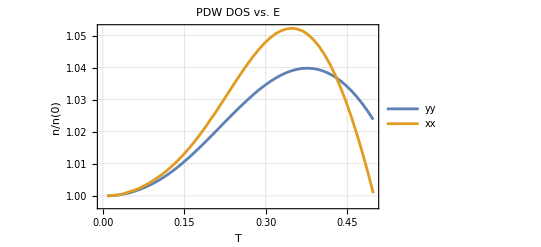

```mathematica
xValues=Range[0.008,0.5,0.01];
Response=Re[Gc+Fc*2+diagm];
FFResponse=Re[(Fc*2)*2-4*Difference];
data=Transpose[{xValues,Response/Response[[1]] }];
data1=Transpose[{xValues,FFResponse}];
data2=Transpose[{xValues,diagm }];
myplot2=ListPlot[{data,dataxx},PlotRange->All,Joined->True,Frame->True,GridLines->Automatic,FrameLabel->{Style["T",20,Bold],Style["n/n(0)",20,Bold]},PlotLabel->"PDW DOS vs. E",PlotLegends->{"yy","xx","Diag"}]
```

```mathematica
sup
```

```mathematica
{x,0.008,0.5,0.01}
```

{x,0.008,0.5,0.01}

```mathematica
First[{x,0.008,0.5,0.01}]
```

x

```mathematica
Difference=Re[{-0.004009209983473996-1.0932292529565122*^-16 ⅈ,-0.004046982329284493-1.130198242562599*^-16 ⅈ,-0.004113822749237786-9.708633583689744*^-17 ⅈ,-0.004207441705914708-6.886135389854273*^-17 ⅈ,-0.004328886498225368-5.596535412803918*^-17 ⅈ,-0.004484600255587487-7.990243841087146*^-17 ⅈ,-0.004668822044361309-7.588407431644213*^-17 ⅈ,-0.004884272955887212-7.998329227593229*^-17 ⅈ,-0.005135610659892098-6.163006570033231*^-17 ⅈ,-0.005420958028526504-8.394787106225855*^-17 ⅈ,-0.00574429104803123-5.815327810103516*^-17 ⅈ,-0.006107997252335143-4.9018505874313897*^-17 ⅈ,-0.006513155458373832-4.3304868802700846*^-17 ⅈ,-0.006964565657989211-5.290316510495707*^-17 ⅈ,-0.007466829519512219-4.407058183426049*^-17 ⅈ,-0.008023511162478597-3.7841723435693145*^-17 ⅈ,-0.008636317542003558-3.989561686302139*^-17 ⅈ,-0.009308481109586014-4.319160639016502*^-17 ⅈ,-0.010045227471375706-4.4718799899759805*^-17 ⅈ,-0.010845223815316357-5.598904951548621*^-17 ⅈ,-0.011713025698149776-4.67174381260419*^-17 ⅈ,-0.012648425050385576-5.843876634568239*^-17 ⅈ,-0.013652042963139766-4.492546895977274*^-17 ⅈ,-0.01472379531947704-4.341103936252301*^-17 ⅈ,-0.015863100756179818-3.7522864108432923*^-17 ⅈ,-0.017068873661277142-3.8141372873812144*^-17 ⅈ,-0.0183397040726892-4.389670632993332*^-17 ⅈ,-0.019673719745168156-4.9283705748387775*^-17 ⅈ,-0.021068719400903685-5.004313352779251*^-17 ⅈ,-0.02252226839174637-5.173827862109739*^-17 ⅈ,-0.02403158304826236-5.202556126079631*^-17 ⅈ,-0.02559368274248161-5.17191214558921*^-17 ⅈ,-0.027205423410871343-4.837663680607149*^-17 ⅈ,-0.028863409353717367-5.671706504890618*^-17 ⅈ,-0.03056443144729054-7.086355793626701*^-17 ⅈ,-0.03230414628956124-7.021259260893108*^-17 ⅈ,-0.03407960714131558-7.095173094729985*^-17 ⅈ,-0.03588692956814349-6.857359928244881*^-17 ⅈ,-0.037722029628497106-7.19991719299179*^-17 ⅈ,-0.03958191698056253-6.767814910776125*^-17 ⅈ,-0.04146147412287739-7.579811304423101*^-17 ⅈ,-0.043358730475436535-7.469025080717664*^-17 ⅈ,-0.04526730768897197-7.196552614297998*^-17 ⅈ,-0.04718587884684387-7.147834925532904*^-17 ⅈ,-0.049110077017548354-7.642378759703905*^-17 ⅈ,-0.05103634148365557-7.566359764479961*^-17 ⅈ,-0.05296124711740986-7.372147482371015*^-17 ⅈ,-0.05488182375905695-7.168987083665726*^-17 ⅈ,-0.0567938593693582-7.280890749992325*^-17 ⅈ,-0.0586952150169138-7.029679594457642*^-17 ⅈ}] ;
```